## AbstractCategory ReducedMorphismAssociation

Here, y•f = h•(g•f) = h•x, but the older ResourceFunction[“AbstractCategory”] doesn’t know this (some morphisms appear double) because it can’t handle non-elementary composition equivalences.

<|f→a->b,g→b->c,h→c->d,i→d->e,x→a->c,y→b->d,y⊙f→a->d,i⊙h→c->e,h⊙x→a->d,i⊙y→b->e,(i⊙y)⊙f→a->e,(i⊙h)⊙g→b->e,(i⊙h)⊙x→a->e,ã→a->a,b̃→b->b,c̃→c->c,d̃→d->d,ẽ→e->e|>

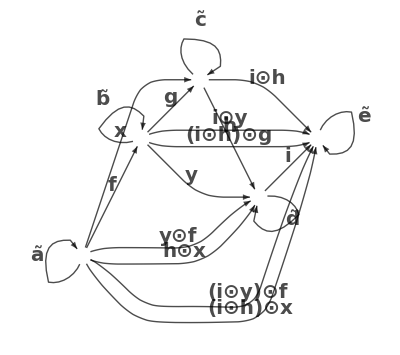

```mathematica
cat=ResourceFunction["AbstractCategory"][<|f->{a,b},g->{b,c},h->{c,d},i->{d,e},x->{a,c},y->{b,d}|>,{},{CircleDot[g,f]==x,CircleDot[h,g]==y}];
cat["ReducedMorphismAssociation"]
cat["ReducedLabeledGraph"]
```

<|f→a->b,g→b->c,h→c->d,i→d->e,x→a->c,y→b->d,y⊙f→a->d,i⊙h→c->e,i⊙y→b->e,(i⊙y)⊙f→a->e,ã→a->a,b̃→b->b,c̃→c->c,d̃→d->d,ẽ→e->e|>

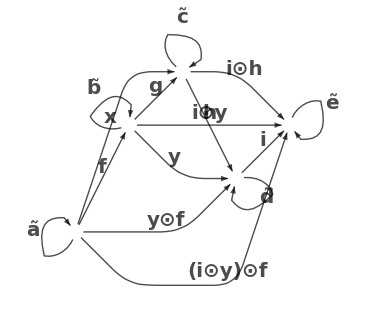

```mathematica
cat=AbstractCategory[<|f->{a,b},g->{b,c},h->{c,d},i->{d,e},x->{a,c},y->{b,d}|>,{},{CircleDot[g,f]==x,CircleDot[h,g]==y}];
cat["ReducedMorphismAssociation"]
cat["ReducedLabeledGraph"]
```